```mathematica
data = Import["/home/jakob/CLionProjects/TST_MKL_Eigen/TST/cmake-build-debug/EigenVectors_M14450_Tres2.csv","CSV"];
```

```mathematica
L = Length[data[[1]]]/2;
v = Table [data[[3,2*k-1]]+I*data[[3,2*k]],{k,1,L}];
w= Table [data[[4,2*k-1]]+I*data[[4,2*k]],{k,1,L}];
Ln = Length[v]/2
v = Normalize[v];
w = Normalize[w];
```

7225

```mathematica
v[[2]]
```

-2.54515×10^-10-3.21673×10^-10 ⅈ

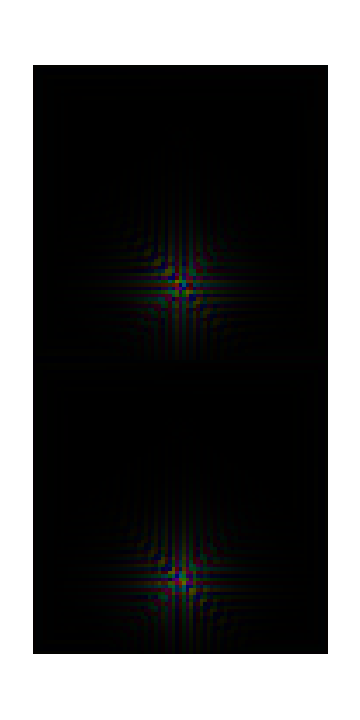
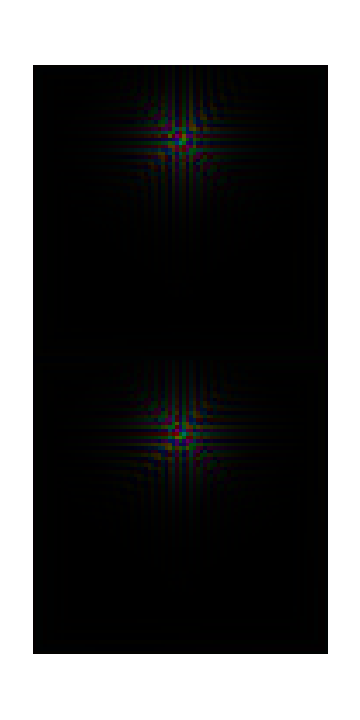

```mathematica
MyPlot[V_] := ArrayPlot[Partition[V,Sqrt[Length[V]/2]],ColorFunction->(Hue[(Arg[#]+π)/(2π) ,1,1-1/(1+Abs[#]^(.2))]&),ColorFunctionScaling->False,ImageSize->Medium];
Row[{MyPlot[v],MyPlot[w]}]
```

```mathematica
MyDot[x_,y_] :=( ∑_(k=1)^(Ln/2) x[[k]]y[[k]]+∑_(k=Ln)^(Ln*3/2) x[[k]]y[[k]]);
```

```mathematica
X =v-(MyDot[v,w]/ MyDot[w,w])w; Y =v-Dot[v,X]/ Dot[X,X]X+w-Dot[w,X]/ Dot[X,X]X;
Row[{MyPlot[Normalize[X]],MyPlot[Normalize[Y]]}]
```

-Graphics--Graphics-

```mathematica
Abs[Normalize[X].Normalize[Y]]
```

3.64498×10^-17

```mathematica
SphericalPlot3D[MyDot[Conjugate[Sin[a]v+Cos[a]*Exp[I b]*w],Sin[a]v+Cos[a]*Exp[I b]*w],{a,0,2π},{b,0,2π}]
```

-Graphics3D-

```mathematica
MyPlot2[V_] := ArrayPlot[Partition[V,Sqrt[Length[V]]],ColorFunction->(Hue[(π+Arg[#])/(2π) ,1,1-1/(1+Abs[#]^(.2))]&),ColorFunctionScaling->False,ImageSize->Medium]
```

```mathematica
Simplify[Re[Norm[Partition[w,Length[w]/2][[1]]-Exp[I a] Partition[v,Length[v]/2][[2]]]]]
```

$Aborted

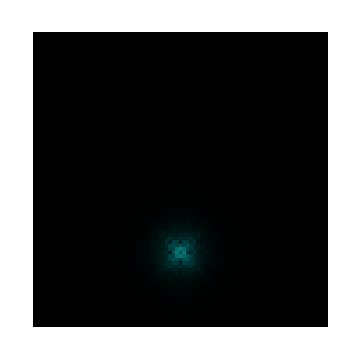
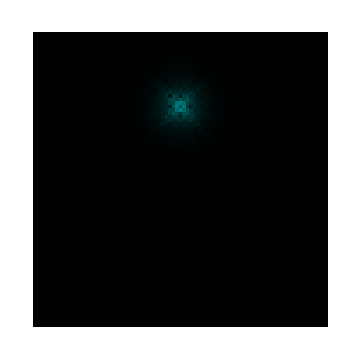

```mathematica
w1 = Partition[w,Length[v]/2][[1]]; w2 = Partition[w,Length[v]/2][[2]];
v1 = Partition[v,Length[v]/2][[1]]; v2 = Partition[v,Length[v]/2][[2]];
Row[{MyPlot2[Normalize[(v1*Conjugate[v1]+v2*Conjugate[v2])] ],MyPlot2[Normalize[(w1*Conjugate[w1]+w2*Conjugate[w2])] ]}]
```